#### Bulk

```mathematica
SetDirectory[NotebookDirectory[]];
<<GRtensors
```

```mathematica
ggValues={{-f[r],1,0},{1,0,0},{0,0,y[r]}};
ggiValues=Inverse[ggValues];
```

```mathematica
SetXMet[{v,r,x1},ggValues,ggiValues];
NewTensor[chris,chrisDef,Simplify]
```

```mathematica
DisplayTensor[gg]//MatrixForm
```

gg[{DownVector,DownVector}] has components

(-f[r] | 1 | 0
1 | 0 | 0
0 | 0 | y[r])

```mathematica
range[DownWS]={1,2};
range[UpWS]={1,2};
```

```mathematica
σaValues={v,r};
σaDef[DefaultIndexType]={UpWS};
σaDef[{a_}]:=σaValues[[a]];
NewTensor[σa,σaDef];
```

```mathematica
XμValues={v,r,x1s[v,r]};
XμDef[DefaultIndexType]={UpVector};
XμDef[{m_}]:=XμValues[[m]];
NewTensor[Xμ,XμDef]
```

```mathematica
dXDef[DefaultIndexType]={DownWS,UpVector};
dXDef[{a_,m_}]:=D[Xμ[{m}],σa[{a}]];
NewTensor[dX,dXDef];
```

```mathematica
habDef[DefaultIndexType]={DownWS,DownWS};
habDef[{a_,b_}]:=Sum[dX[{a,m}]dX[{b,n}]gg[{m,n}],{m,1,dim},{n,1,dim}]/.{x1:>x1s[v,r]};
NewTensor[hab,habDef,Simplify]
```

```mathematica
deth=Simplify[Det[DisplayTensor[hab]]];
```

hab[{DownWS,DownWS}] has components

#### Bulk covariant equations

```mathematica
hRule={h->Function[{v,r},1+f[r] y[r] (Derivative[0,1][x1s][v,r])^2+2 y[r] Derivative[0,1][x1s][v,r] Derivative[1,0][x1s][v,r]]};
```

```mathematica
habInverseValues=1/h[v,r](h[v,r]/.hRule)Simplify[Inverse[DisplayTensor[hab]]]//Simplify;
```

hab[{DownWS,DownWS}] has components

```mathematica
PμaValues=-τf Simplify[Sqrt[h[v,r]]habInverseValues . DisplayTensor[dX] . (DisplayTensor[gg]/.{x1->x1s[v,r]})];
```

dX[{DownWS,UpVector}] has components

gg[{DownVector,DownVector}] has components

```mathematica
PμaDef[DefaultIndexType]={DownVector,UpWS};
PμaDef[{m_,a_}]:=PμaValues[[a,m]];
NewTensor[Pμa,PμaDef]
```

```mathematica
PμaSymbolicValues={{Pvv[v,r],Pvx[v,r]},{Prv[v,r],Prx[v,r]},{Pxv[v,r],Pxr[v,r]}};
PμaSymbolicDef[DefaultIndexType]={DownVector,UpWS};
PμaSymbolicDef[{m_,a_}]:=PμaSymbolicValues[[m,a]];
NewTensor[PμaSymbolic,PμaSymbolicDef];
```

```mathematica
PRules=Flatten[Table[Head[PμaSymbolic[{m,a}]]->Function[{v,r},Evaluate[Pμa[{m,a}]]],{m,1,dim},{a,1,2}]];
```

```mathematica
dPSymbolicDef[DefaultIndexType]={DownVector};
dPSymbolicDef[{m_}]:=Sum[D[PμaSymbolic[{m,a}],σa[{a}]],{a,1,2}];
NewTensor[dPSymbolic,dPSymbolicDef,Simplify];
```

```mathematica
PeomDef[DefaultIndexType]={DownVector};
PeomDef[{m_}]:=dPSymbolic[{m}]-Sum[chris[{m,k,l}]dX[{a,l}]Pμa[{k,a}],{k,1,dim},{l,1,dim},{a,1,2}]/.{x1->x1s[v,r]};
NewTensor[Peom,PeomDef,Simplify]
```

#### Process bulk equations into a useful form

Numerical scheme: Start knowing x1s and Pxv on a time slice, and figure out h and Pxr on the way to obtaining the v derivatives of x1s and Pxv.

```mathematica
hSolve=Solve[Pxv[v,r]==Pμa[{3,1}],h[v,r]][[1]];
hSimp[exp_]:=Assuming[τf>0&&y[r]>0&&Derivative[0,1][x1s][v,r]<0&&Pxv[v,r]>0,Simplify[exp/.hSolve]];
ShouldBeZero=hSimp[PμaSymbolic[{3,1}]-Pμa[{3,1}]]
```

0

```mathematica
x1spRule=hSimp[Solve[(h[v,r]/.hRule)==h[v,r],Derivative[1,0][x1s][v,r]][[1]]];
```

```mathematica
PxrRule=hSimp[{Pxr[v,r]->Pμa[{3,2}]}/.x1spRule];
```

```mathematica
PxvpRule=Solve[Peom[{3}]==0,Derivative[1,0][Pxv][v,r]][[1]];
```

Check the hanging string solution:

```mathematica
x1Hanging[v_,r_]:=β (v-ArcTan[r])
```

```mathematica
AdSSchRules={y->Function[r,r^2],f->Function[r,r^2(1-1/r^4)]};
```

```mathematica
PxvHanging[v_,r_]:=Evaluate[Simplify[Pxv[v,r]/.PRules/.hRule/.AdSSchRules/.{x1s->x1Hanging}]]
```

```mathematica
PxrHanging[v_,r_]:=Evaluate[Simplify[Pxr[v,r]/.PRules/.hRule/.AdSSchRules/.{x1s->x1Hanging}]]
```

```mathematica
ShouldBeZero=Derivative[1,0][x1Hanging][v,r]-Simplify[Derivative[1,0][x1s][v,r]/.x1spRule/.AdSSchRules/.{x1s->x1Hanging,Pxv->PxvHanging}]
ShouldBeZero=Simplify[Derivative[1,0][Pxv][v,r]/.PxvpRule/.{Pxr->Function[{v,r},Evaluate[Pxr[v,r]/.PxrRule]]}/.AdSSchRules/.{x1s->x1Hanging,Pxv->PxvHanging}]
```

0

0

#### Covariant treatment of endpoints

```mathematica
XμAValues={v,rA[v],x1A[v]};
XμADef[DefaultIndexType]={UpVector};
XμADef[{m_}]:=XμAValues[[m]];
NewTensor[XμA,XμADef]
```

```mathematica
dXADef[DefaultIndexType]={UpVector};
dXADef[{m_}]:=D[XμA[{m}],v];
NewTensor[dXA,dXADef]
```

```mathematica
σAaValues={v,rA[v]};
σAaDef[DefaultIndexType]={UpWS};
σAaDef[{a_}]:=σAaValues[[a]];
NewTensor[σAa,σAaDef];
```

```mathematica
dσADef[DefaultIndexType]={UpWS};
dσADef[{a_}]:=D[σAa[{a}],v];
NewTensor[dσA,dσADef];
```

```mathematica
pμADef[DefaultIndexType]={DownVector};
pμADef[{m_}]:=1/ηA[v]Sum[gg[{m,n}]dXA[{n}]/.{r->rA[v]},{n,1,dim}];
NewTensor[pμA,pμADef];
```

```mathematica
pμASymbolicValues={pvA[v],prA[v],pxA[v]};
pμASymbolicDef[DefaultIndexType]={DownVector};
pμASymbolicDef[{m_}]:=pμASymbolicValues[[m]];
NewTensor[pμASymbolic,pμASymbolicDef];
pARules=Table[Head[pμASymbolic[{m}]]->Function[v,Evaluate[pμA[{m}]]],{m,1,dim}];
```

```mathematica
ϵabValues={{0,1},{-1,0}};
ϵabDef[DefaultIndexType]={DownWS,DownWS};
ϵabDef[{a_,b_}]:=ϵabValues[[a,b]];
NewTensor[ϵab,ϵabDef];
```

```mathematica
pAeomDef[DefaultIndexType]={DownVector};
pAeomDef[{m_}]:=D[pμASymbolic[{m}],v]-Sum[chris[{m,k,l}]dXA[{l}]pμA[{k}],{k,1,dim},{l,1,dim}]-Sum[dσA[{a}]ϵab[{a,b}]Pμa[{m,b}],{a,1,2},{b,1,2}]/.{r->rA[v]};
NewTensor[pAeom,pAeomDef,Simplify]
```

#### Process endpoint equations into useful forms, 2nd try

Lightlike condition at the endpoint:

```mathematica
rApRule=Solve[(Sum[gg[{m,n}]dXA[{m}]dXA[{n}],{m,1,dim},{n,1,dim}]/.{r->rA[v]})==0,rA'[v]][[1]];
```

Use the defining expressions for the momenta to find expressions for η and x1’.

```mathematica
ηARule={ηA->Function[v,Evaluate[ηA[v]/.Solve[pμASymbolic[{2}]==pμA[{2}],ηA[v]][[1]]]]};
```

```mathematica
xApRule=Solve[pμASymbolic[{3}]==pμA[{3}],x1A'[v]][[1]]/.ηARule;
```

```mathematica
pvARule={pμASymbolic[{1}]->Simplify[pμA[{1}]/.rApRule/.xApRule/.ηARule]};
pvAFunctionRule={pvA->Function[v,Evaluate[pvA[v]/.pvARule]]};
```

By matching x1’ at the boundary to the appropriate expression from the bulk of the string, we get an explicit expression for P_x^v at the endpoint.  There is a sign ambiguity, and the sign choice we make causes px’[v] to be negative when px[v] and pr[v] are positive.

```mathematica
prpRule=Simplify[Solve[hSimp[pAeom[{2}]/.xApRule/.{rA[v]->r}]==0,prA'[v]][[1]]/.rApRule/.xApRule/.ηARule/.x1spRule/.{rA[v]->r}];
```

```mathematica
pxpRule=Simplify[Solve[hSimp[pAeom[{3}]/.{rA[v]->r}]==0,pxA'[v]][[1]]/.x1spRule/.rApRule/.xApRule]/.{rA[v]->r};
```

#### Alternative formula for rA’

```mathematica
x1AConsistencyRule={x1A'[v]->D[x1s[v,rA[v]],v]};
```

```mathematica
Simplify[Solve[rA'[v]==(rA'[v]/.rApRule/.x1AConsistencyRule),rA'[v]]] (* obtain rA' from the lightlike constraint eq. by using the x1A' in terms of rA' *)
```

{{rA'[v]→-(1+y[rA[v]] x1s^(0,1)[v,rA[v]] x1s^(1,0)[v,rA[v]]+√(1+f[rA[v]] y[rA[v]] (x1s^(0,1)[v,rA[v]])^2+2 y[rA[v]] x1s^(0,1)[v,rA[v]] x1s^(1,0)[v,rA[v]]))/(y[rA[v]] (x1s^(0,1)[v,rA[v]])^2)},{rA'[v]→(-1-y[rA[v]] x1s^(0,1)[v,rA[v]] x1s^(1,0)[v,rA[v]]+√(1+f[rA[v]] y[rA[v]] (x1s^(0,1)[v,rA[v]])^2+2 y[rA[v]] x1s^(0,1)[v,rA[v]] x1s^(1,0)[v,rA[v]]))/(y[rA[v]] (x1s^(0,1)[v,rA[v]])^2)}}

```mathematica
rApAltRule={rA'[v]->1/(y[rA[v]] (Derivative[0,1][x1s][v,rA[v]])^2)(-1-y[rA[v]] Derivative[0,1][x1s][v,rA[v]] Derivative[1,0][x1s][v,rA[v]]+ϵ*√(1+f[rA[v]] y[rA[v]] (Derivative[0,1][x1s][v,rA[v]])^2+2 y[rA[v]] Derivative[0,1][x1s][v,rA[v]] Derivative[1,0][x1s][v,rA[v]]))}; (* write the general solution with an ϵ that can take +1, -1 values *)
```

```mathematica
x1ApAltRule=Simplify[x1AConsistencyRule/.rApAltRule]
```

{x1A'[v]→(-1+ϵ √(1+f[rA[v]] y[rA[v]] (x1s^(0,1)[v,rA[v]])^2+2 y[rA[v]] x1s^(0,1)[v,rA[v]] x1s^(1,0)[v,rA[v]]))/(y[rA[v]] x1s^(0,1)[v,rA[v]])}

#### Using this, we get EoMs that depend on ϵ (for ϵ=+1 we get the old prpRuleBetter and pxpRuleBetter)

```mathematica
x1spAltRule={Derivative[1,0][x1s]->Function[{v,r},(-1+h[v,r]-f[r] y[r] (Derivative[0,1][x1s][v,r])^2)/(2 y[r] Derivative[0,1][x1s][v,r])]};
```

```mathematica
hRuleX=Solve[x1A'[v]==(x1A'[v]/.x1ApAltRule/.x1spAltRule/.√h[v,rA[v]]->x),x][[1]]/.ϵ->1/ϵ;
```

```mathematica
pxEOMRule=Simplify[Solve[(Simplify[Assuming[h[v,rA[v]]>0,Simplify[Simplify[pAeom[{3}]/.rApAltRule/.hRule]/.x1spAltRule]]/.Sqrt[h[v,rA[v]]]->x/.hRuleX]/.xApRule)==0,pxA'[v]]][[1]]
```

{pxA'[v]→-(ϵ τf pxA[v])/prA[v]}

```mathematica
prEOMRule=Simplify[Solve[Simplify[Assuming[h[v,rA[v]]>0,Simplify[Simplify[pAeom[{2}]/.rApAltRule/.hRule]/.x1spAltRule]]/.Sqrt[h[v,rA[v]]]->x/.hRuleX/.ηARule/.xApRule]==0,prA'[v]]][[1]]/.rA[v]->r
```

{prA'[v]→1/2 (-2 ϵ τf-prA[v] f'[r]+(pxA[v]^2 y'[r])/(prA[v] y[r]^2))}

#### Overall structure of equations of motion

Convert the bulk and boundary differential equations into a set of rules BulkRules for bulk quantities and another set of rules BoundaryLineRules for boundary quantities.  These rules are in a form that is convenient for discretization.

```mathematica
AllLineRules={Derivative[1,0][x1s][v,r]->x1'[v]-r'[v]drx[v],Derivative[0,1][x1s][v,r]->drx[v],Derivative[0,1][Pxr][v,r]->drPxr[v],Derivative[1,0][Pxv][v,r]->Pxv'[v]-r'[v]drPxv[v],Pxr[v,r]->Pxr[v],Pxv[v,r]->Pxv[v],x1s[v,r]->x1[v],h[v,r]->h[v],x1A->x1,rA->r,y[r]->y[r[v]],f[r]->f[r[v]]};
```

```mathematica
BVD={{x1,drx,x1N},{r,drr,rN},{Pxr,drPxr,PxrN},{Pxv,drPxv,PxvN}};
BDZRules=Table[BVD[[i,2]]->(0&),{i,1,Length[BVD]}];
```

```mathematica
x1pLineRule=Simplify[Solve[(Derivative[1,0][x1s][v,r]-(Derivative[1,0][x1s][v,r]/.x1spRule)/.AllLineRules)==0,x1'[v]][[1]]];
```

```mathematica
PxrLineRule=Simplify[Solve[(Pxr[v,r]-(Pxr[v,r]/.PxrRule)/.AllLineRules)==0,Pxr[v]][[1]]];
```

```mathematica
PxvpLineRule=Simplify[Solve[(Derivative[1,0][Pxv][v,r]-(Derivative[1,0][Pxv][v,r]/.PxvpRule)/.AllLineRules)==0,Pxv'[v]][[1]]];
```

```mathematica
BulkLineRules=Flatten[{x1pLineRule,PxrLineRule,PxvpLineRule}];
```

```mathematica
rApLineRule=Simplify[rApRule/.xApRule/.AllLineRules];
```

```mathematica
rApLineAltRule=Simplify[rApAltRule/.rA->r/.r[v]->r/.x1spRule/.Derivative[0,1][x1s][v,r]->drx[v]/.Pxr[v,r]->Pxr[v]/.Pxv[v,r]->Pxv[v]/.y[r]->y[r[v]]/.f[r]->f[r[v]]];
```

```mathematica
xApLineRule={x1'[v]->Simplify[hSimp[x1A'[v]/.xApRule/.AllLineRules]/.{r[v]->r}]/.AllLineRules};
```

```mathematica
xApLineAltRule=Simplify[x1ApAltRule/.x1A->x1/.rA->r/.r[v]->r/.x1spRule/.Derivative[0,1][x1s][v,r]->drx[v]/.Pxr[v,r]->Pxr[v]/.Pxv[v,r]->Pxv[v]/.y[r]->y[r[v]]/.f[r]->f[r[v]]];
```

```mathematica
prpLineAltRule=Simplify[prEOMRule/.{Derivative[0,1][x1s][v,rA[v]]->Derivative[0,1][x1s][v,r]}/.AllLineRules/.{Pxv[v,r[v]]->Pxv[v]}]/.{f$_[r]->f$[r[v]]};
```

```mathematica
pxpLineAltRule=pxEOMRule/.AllLineRules/.{f$_[r]->f$[r[v]]};
```

```mathematica
(*PxvEndpointLineAltRule={Pxv[v]->-(ϵ τf drx[v] y[rGeo[v]])/(1+drx[v] y[rGeo[v]] x1Geo'[v])};*)
```

```mathematica
PxvEndpointLineAltRule={Pxv[v]->-(ϵ τf y[rGeo[v]])/(1/drx[v]+y[rGeo[v]] x1Geo'[v])};
```

Here we include the ϵ in the boundary equations of motion for px and pr, as well as in the matching condition for Pxv and the endpoint

#### Pseudospectral discretization

```mathematica
BVD={{r,drr,rN},{x1,drx,x1N},{Pxr,drPxr,PxrN},{Pxv,drPxv,PxvN}};
BDZRules=Table[BVD[[i,2]]->(0&),{i,1,Length[BVD]}];
BdyVD={{prA,prAN},{pxA,pxAN}};
```

```mathematica
NumPoints=12;
```

```mathematica
uj$=N[Table[Cos[π(j-1)/NumPoints],{j,1,NumPoints+1}],20];
pj$=Table[If[(j==1)||(j==NumPoints+1),2,1],{j,1,NumPoints+1}];
dij$=IdentityMatrix[NumPoints+1];
dij$[[1,1]]=(1+2NumPoints^2)/6;
dij$[[NumPoints+1,NumPoints+1]]=-(1+2NumPoints^2)/6;
Do[dij$[[j,j]]=-uj$[[j]]/(2(1-uj$[[j]]^2)),{j,2,NumPoints}];
Do[If[i≠j,dij$[[i,j]]=(-1)^(i+j)pj$[[i]]/(pj$[[j]](uj$[[i]]-uj$[[j]]))],{i,1,NumPoints+1},{j,1,NumPoints+1}];
rj$=N[rH+(rEndSymbolic-rH)/2(uj$+1)/.AdSSchRules]/.{rEndSymbolic->rGeo[v]};
```

For testing it’s nice to have a symbolic form:

```mathematica
VarReplaceRules[j_]:=Flatten[Table[{BVD[[i,1]][v]->BVD[[i,3]][j][v],BVD[[i,1]]'[v]->BVD[[i,3]][j]'[v]},{i,1,Length[BVD]}]];
DerivReplaceRules[j_,Np_]:=Table[BVD[[i,2]][v]->2/(rGeo[v]-rH)Sum[dij$[[Np+1-j,Np+1-k]]BVD[[i,3]][k][v],{k,0,Np}],{i,1,Length[BVD]}]/.x1N[NumPoints][v]->x1Geo[v];
BdyReplaceRules[]:=Table[BdyVD[[i,1]]->BdyVD[[i,2]],{i,1,Length[BdyVD]}];
rGaugeTable=Table[rN[j]->Function[v,Evaluate[rj$[[NumPoints+1-j]]]],{j,0,NumPoints}];
DiscretizeLines[exp_,j_,Np_]:=exp/.VarReplaceRules[j]/.DerivReplaceRules[j,Np]/.BdyReplaceRules[]/.rGaugeTable;
```

x1 discretization: use bulk equation except at the boundary.  (First order everywhere).

```mathematica
xDiscretizations=Table[DiscretizeLines[x1'[v]-(x1'[v]/.BulkLineRules),j,NumPoints],{j,0,NumPoints-1}];
```

Pxr discretization: from bulk equations of motion everywhere.  (Algebraic everywhere).

```mathematica
PxrDiscretizations=Table[DiscretizeLines[Pxr[v]-(Pxr[v]/.BulkLineRules),j,NumPoints],{j,0,NumPoints}];
```

Pxv discretization: from bulk equations except at boundary.  (First order except at boundary where it’s algebraic).

```mathematica
PxvDiscretizationsWithoutEndpointRule=Table[DiscretizeLines[Pxv'[v]-(Pxv'[v]/.BulkLineRules),j,NumPoints],{j,0,NumPoints}];
```

```mathematica
PxvDiscretizationsWithEndpointRule=Join[Table[DiscretizeLines[Pxv'[v]-(Pxv'[v]/.BulkLineRules),j,NumPoints],{j,0,NumPoints-1}],{DiscretizeLines[Pxv[v]-(Pxv[v]/.PxvEndpointLineAltRule),NumPoints,NumPoints]}];
```

```mathematica
AllDiscretizationsWithoutEndpointRule=Flatten[{xDiscretizations,PxrDiscretizations,PxvDiscretizationsWithoutEndpointRule}]/.AdSSchRules;
AllDiscretizationsWithEndpointRule=Flatten[{xDiscretizations,PxrDiscretizations,PxvDiscretizationsWithEndpointRule}]/.AdSSchRules;
AllDiscreteVars=Flatten[Join[Table[{PxrN[j],PxvN[j]},{j,0,NumPoints}],Table[x1N[j],{j,0,NumPoints-1}]]];
```

```mathematica
AdSSchRules={y->Function[r,r^2],f->Function[r,r^2-1/r^2],rH->1};
```

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
StartPoint[SolnRule_] := InterpolatingFunctionDomain[SolnRule[[1,2]]][[1,1]];
EndPoint[SolnRule_] := InterpolatingFunctionDomain[SolnRule[[1,2]]][[1,2]];
FindTimeSteps[soln_]:=Length[InterpolatingFunctionGrid[soln[[1,1]]/.soln[[1]]]]
```

#### Null geodesic

```mathematica
pGeoValues={pvGeo,prGeo[ξ],px1Geo};
pGeoDef[DefaultIndexType]={DownVector};
pGeoDef[{m_}]:=pGeoValues[[m]];
NewTensor[pGeo,pGeoDef]
```

```mathematica
prGeoRules=Solve[(Sum[gg[{{m,UpVector},{n,UpVector}}]pGeo[{m}]pGeo[{n}],{m,1,dim},{n,1,dim}]/.{r->rGeo[ξ]})==0,prGeo[ξ]]
```

{{prGeo[ξ]→(-pvGeo y[rGeo[ξ]]-√(-px1Geo^2 f[rGeo[ξ]] y[rGeo[ξ]]+pvGeo^2 y[rGeo[ξ]]^2))/(f[rGeo[ξ]] y[rGeo[ξ]])},{prGeo[ξ]→(-pvGeo y[rGeo[ξ]]+√(-px1Geo^2 f[rGeo[ξ]] y[rGeo[ξ]]+pvGeo^2 y[rGeo[ξ]]^2))/(f[rGeo[ξ]] y[rGeo[ξ]])}}

```mathematica
xGeoValues={vGeo[ξ],rGeo[ξ],x1Geo[ξ]};
xGeoDef[DefaultIndexType]={UpVector};
xGeoDef[{m_}]:=xGeoValues[[m]];
NewTensor[xGeo,xGeoDef]
```

```mathematica
xGeoDotDef[DefaultIndexType]={UpVector};
xGeoDotDef[{m_}]:=D[xGeo[{m}],ξ];
NewTensor[xGeoDot,xGeoDotDef];
```

```mathematica
LagGeo=1/(2η[ξ])Sum[gg[{m,n}]xGeoDot[{m}]xGeoDot[{n}],{m,1,dim},{n,1,dim}]-1/2m^2η[ξ]/.{r->rGeo[ξ]};
```

Here are expressions for the conjugate momentum in terms of position and velocity:

```mathematica
pvGeoValue=Simplify[D[LagGeo,vGeo'[ξ]]];
px1GeoValue=Simplify[D[LagGeo,x1Geo'[ξ]]];
prGeoValue=Simplify[D[LagGeo,rGeo'[ξ]]];
```

A choice of two gauges:

```mathematica
vGaugeChoice={vGeo'[ξ]->1};
rGaugeChoice={rGeo'[ξ]->1};
```

Either way, we can eliminate η in favor of p_r:

```mathematica
ηRule=Solve[prGeoValue==prGeo[ξ],η[ξ]][[1]];
```

```mathematica
lag=LagGeo/.{m->0}/.vGaugeChoice/.{ξ->v};
```

```mathematica
eoms={D[lag,η[v]],D[lag,rGeo[v]]-D[lag,rGeo'[v],v],D[lag,x1Geo[v]]-D[lag,x1Geo'[v],v]};
```

The equations of motion are second order in x_1, so we need initial conditions for x_1 (trivial, we start at x_1=0) and (ẋ)_1 (from p_x_1=1).  They are first order in η, so we need initial conditions for η (from ηRule).  And they’re first order in r, so we need initial conditions for r.  You can’t choose r=1.
Here we have a choice whether the geodesic goes up or down, plus I also added the initial x as a variable in the MakeGeo procedure.

```mathematica
η0RuleUp=Simplify[ηRule/.vGaugeChoice/.prGeoRules[[2]]/.{ξ->0}/.AdSSchRules/.{rGeo[0]->rGeo0}/.{px1Geo->1}];
η0RuleDown=Simplify[ηRule/.vGaugeChoice/.prGeoRules[[1]]/.{ξ->0}/.AdSSchRules/.{rGeo[0]->rGeo0}/.{px1Geo->1}];
```

```mathematica
tmpUp=Join[Simplify[eoms/.AdSSchRules],{η[0]-(η[0]/.η0RuleUp)/.{rGeo[0]->rGeo0},x1Geo'[0]-(x1Geo'[ξ]/.Solve[px1GeoValue==1,x1Geo'[ξ]][[1]]/.{ξ->0}/.AdSSchRules/.η0RuleUp)/.{rGeo[0]->rGeo0},x1Geo[0]-x1Geo0,rGeo[0]-rGeo0}];
ebcsGeoUp=Table[tmpUp[[i]]==0,{i,1,Length[tmpUp]}];
```

```mathematica
tmpDown=Join[Simplify[eoms/.AdSSchRules],{η[0]-(η[0]/.η0RuleDown)/.{rGeo[0]->rGeo0},x1Geo'[0]-(x1Geo'[ξ]/.Solve[px1GeoValue==1,x1Geo'[ξ]][[1]]/.{ξ->0}/.AdSSchRules/.η0RuleDown)/.{rGeo[0]->rGeo0},x1Geo[0]-x1Geo0,rGeo[0]-rGeo0}];
ebcsGeoDown=Table[tmpDown[[i]]==0,{i,1,Length[tmpDown]}];
```

ebcsGeo comprises the equations of motion and boundary conditions needed to produce a null geodesic.  You have to specify the initial radius rGeo0 and the initial energy, p_v<0.  We always start at x_1=0 and with the more positive (i.e. upward) of the two choices of p_r.  The “EventLocator” option allows us to stop the integration just at the moment when we cross the horizon.

```mathematica
ClearAll[MakeGeoUp];
MakeGeoUp[Myx10_,Myr0_,Mypv_,MyvMax_:10]:=
(
solnGeoUp=Apply[NDSolve,{ebcsGeoUp/.{x1Geo0->Myx10,rGeo0->Myr0,pvGeo->Mypv},{x1Geo,rGeo,η},{v,0,MyvMax},Method->{"EventLocator","Event"->rGeo[v]-1}}][[1]];
)
```

```mathematica
ClearAll[MakeGeoDown];
MakeGeoDown[Myx10_,Myr0_,Mypv_,MyvMax_:10]:=
(
solnGeoDown=Apply[NDSolve,{ebcsGeoDown/.{x1Geo0->Myx10,rGeo0->Myr0,pvGeo->Mypv},{x1Geo,rGeo,η},{v,0,MyvMax},Method->{"EventLocator","Event"->rGeo[v]-1}}][[1]];
)
```

```mathematica
ShowGeo[soln_]:=
ParametricPlot[{x1Geo[v],rGeo[v]}/.soln,{v,0,EndPoint[soln]},AspectRatio->1/GoldenRatio]
```

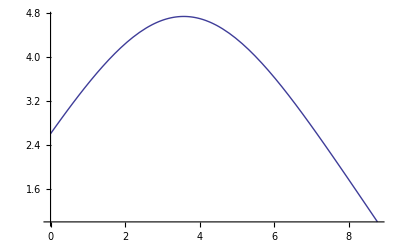

```mathematica
MakeGeoUp[0,2.6,-0.999];
ShowGeo[solnGeoUp]
```

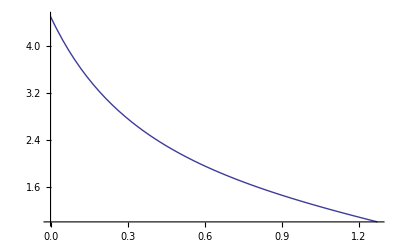

```mathematica
MakeGeoDown[0,4.5,-1.1];
ShowGeo[solnGeoDown]
```

```mathematica
pvRule=Solve[pr==1/f[r](√(pv^2-px^2 f[r]/y[r])-pv),pv][[1]]
```

{pv→(-px^2-pr^2 f[r] y[r])/(2 pr y[r])}

#### Initial conditions and the execution of the code

```mathematica
rEndInitial=2;
pxInitial=1.4;
prInitial=0.46;
τfChosen=1/10;
AdSSchRules={y->Function[r,r^2],f->Function[r,r^2-1/r^2],rH->1,τf->τfChosen};
βRule={β->Sqrt[f[rEndInitial]/y[rEndInitial]]};
```

Initial pv of the geodesic

```mathematica
RNum=(pv/px)/.pvRule/.AdSSchRules/.r->rEndInitial/.px->pxInitial/.pr->prInitial
```

-0.996506

```mathematica
RNum==(√(f[r]/y[r])/.AdSSchRules)
```

-0.996506==√((-1/r^2+r^2)/r^2)

```mathematica
NSolve[-RNum==(√(f[r]/y[r])/.AdSSchRules),r]
```

{{r→-3.46026},{r→0.+3.46026 ⅈ},{r→0.-3.46026 ⅈ},{r→3.46026}}

```mathematica
βRuleClear={β->Sqrt[f[r]/y[r]]};
```

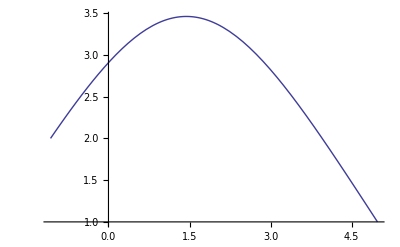

```mathematica
MakeGeoUp[x1Hanging[0,r]/.βRuleClear/.AdSSchRules/.r->rEndInitial,rEndInitial,RNum]
ShowGeo[solnGeoUp]
```

```mathematica
PxvEndFactor=FullSimplify[(PxvEndpointLineAltRule/.{drx[v]->D[x1Hanging[v,r],r]/.βRule/.AdSSchRules/.r->rEndInitial}/.rGeo[v]->rEndInitial/.AdSSchRules/.solnGeoUp/.v->0)[[1,2]]/(PxvHanging[0,r]/.βRule/.AdSSchRules)]/.r->rEndInitial/.ϵ->1;
```

```mathematica
InitialConditions=Flatten[{Table[x1N[j][0]-x1Hanging[0,rN[j][0]/.rGaugeTable],{j,0,NumPoints-1}],Table[PxvN[j][0]-PxvEndFactor*PxvHanging[0,rN[j][0]/.rGaugeTable],{j,0,NumPoints-1}]}]/.βRule/.AdSSchRules/.(ϵ->+1)/.solnGeoUp;
```

```mathematica
AllExpressions=Flatten[{AllDiscretizationsWithEndpointRule,InitialConditions}]/.AdSSchRules/.(ϵ->+1)/.solnGeoUp;
```

```mathematica
ndsArgs={Table[AllExpressions[[i]]==0,{i,1,Length[AllExpressions]}],AllDiscreteVars,{v,0,EndPoint[solnGeoUp]}};
soln=Apply[NDSolve,ndsArgs][[1]];
```

NDSolve::ndsz: At v == 5.80205, step size is effectively zero; singularity or stiff system suspected.

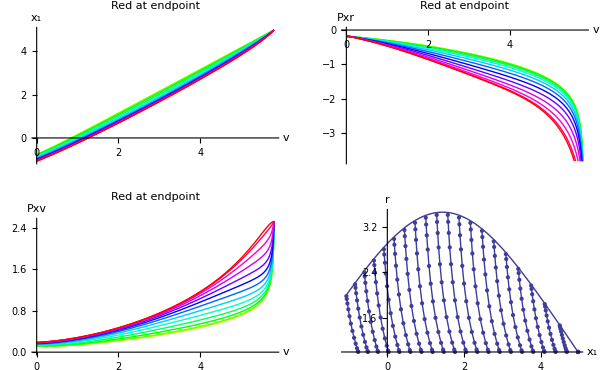

```mathematica
xNPlots=Plot[Evaluate[Flatten[{Table[x1N[i][v]/.soln,{i,0,NumPoints-1}],x1Geo[v]/.solnGeoUp}]],{v,0,EndPoint[soln]},AxesLabel->{"v","x_1"},PlotStyle->Table[Hue[0.2+0.8i/NumPoints],{i,0,NumPoints}],PlotLabel->"Red at endpoint"];
PxrPlots=Plot[Evaluate[Table[PxrN[i][v]/.soln,{i,0,NumPoints}]],{v,0,EndPoint[soln]},AxesLabel->{"v","Pxr"},PlotStyle->Table[Hue[0.2+0.8i/NumPoints],{i,0,NumPoints}],PlotLabel->"Red at endpoint"];
PxvPlots=Plot[Evaluate[Flatten[{Table[PxvN[i][v]/.soln,{i,0,NumPoints}]}]],{v,0,EndPoint[soln]},AxesLabel->{"v","Pxv"},PlotStyle->Table[Hue[0.2+0.8i/NumPoints],{i,0,NumPoints}],PlotLabel->"Red at endpoint"];
StringPlots=Show[ShowGeo[solnGeoUp],Table[ListPlot[Table[{x1N[j][v],rN[j][v]},{j,0,NumPoints-1}]/.rGaugeTable/.solnGeoUp/.AdSSchRules/.soln/.{v->vFrac EndPoint[soln]},PlotRange->{{-1,6},{0.9,4}},AxesOrigin->{0,1},Joined->True,Mesh->Full],{vFrac,0,1,0.05}],AxesLabel->{"x_1","r"}];
GraphicsGrid[{{xNPlots,PxrPlots},{PxvPlots,StringPlots}},ImageSize->600]
```

```mathematica
Append[Table[{x1N[j][v],rN[j][v]},{j,0,NumPoints}],{x1Geo[v],rGeo[v]}/.solnGeoUp]
```

{{x1N[0][v],rN[0][v]},{x1N[1][v],rN[1][v]},{x1N[2][v],rN[2][v]},{x1N[3][v],rN[3][v]},{x1N[4][v],rN[4][v]},{x1N[5][v],rN[5][v]},{x1N[6][v],rN[6][v]},{x1N[7][v],rN[7][v]},{x1N[8][v],rN[8][v]},{x1N[9][v],rN[9][v]},{x1N[10][v],rN[10][v]},{x1N[11][v],rN[11][v]},{x1N[12][v],rN[12][v]},{InterpolatingFunction[{{0.,5.80215}},<>][v],InterpolatingFunction[{{0.,5.80215}},<>][v]}}

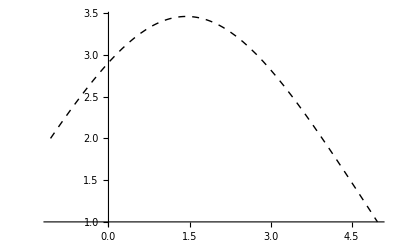

```mathematica
ParametricPlot[{x1Geo[v],rGeo[v]}/.solnGeoUp,{v,0,EndPoint[solnGeoUp]},AspectRatio->1/GoldenRatio,PlotStyle->{Thick,Black,Dashed}]
```

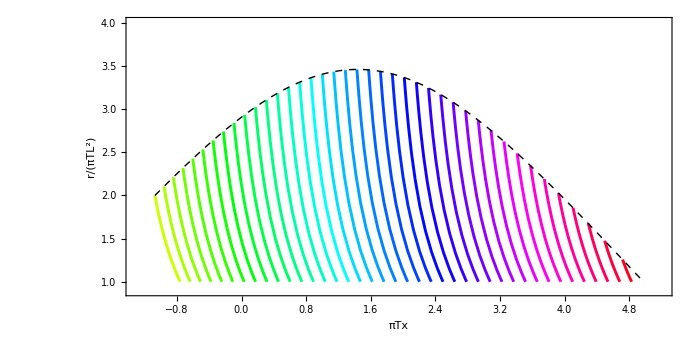

```mathematica
ForExport=Show[Table[ListPlot[Append[Table[{x1N[j][v],rN[j][v]},{j,0,NumPoints-1}],{x1Geo[v],rGeo[v]}/.solnGeoUp]/.rGaugeTable/.solnGeoUp/.AdSSchRules/.soln/.{v->vFrac EndPoint[soln]},PlotStyle->{Hue[0.2+0.8vFrac],Thickness[0.003]},PlotRange->{{-1.3,5.2},{0.9,4}},AxesOrigin->{0,1},Joined->True],{vFrac,0,1,0.025}],ParametricPlot[{x1Geo[v],rGeo[v]}/.solnGeoUp,{v,0,EndPoint[solnGeoUp]},AspectRatio->1/GoldenRatio,PlotStyle->{Thick,Black,Dashed}],ImageSize->700,AspectRatio->.5,Axes->False,Frame->True,FrameLabel->{Style["πTx",FontSize->15,Italic,Bold],Style["r/(πTL^2)",FontSize->15,Italic,Bold]},LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},RotateLabel->True]
```

```mathematica
Export["StringShapesEF.pdf",ForExport]
```

StringShapesEF.pdf

#### Here we treat the snap-back

RHS of eq. (63) in Steve’s notes is determined solely by the null geodesic, so we can find when the px momentum gets depleted either by using the analytical (6.2) from my notes, or since we already have the relevant geodesic in a numerically, we can extract it from there (this is all confirmed by the full code that takes into account the momentum equations as well)

```mathematica
xForce[vv_]:=y[rGeo[v]]x1Geo'[v]/.AdSSchRules/.solnGeoUp/.v->vv;
```

```mathematica
vTrans=If[pxInitial/τfChosen<NIntegrate[xForce[v],{v,0,EndPoint[solnGeoUp]}],Quiet[FindRoot[pxInitial/τfChosen==NIntegrate[xForce[v],{v,0,vTrans}],{vTrans,EndPoint[solnGeoUp]/2}]]][[1,2]]
```

2.05954

Endpoint is at the following radial position when the snapback occurs:

```mathematica
rEndInitialNew=rGeo[vTrans]/.solnGeoUp
```

3.32401

Pseudospectralmethods give for the derivative at v=vTrans at the endpoint:

```mathematica
drxPseudo=drx[v]/.DerivReplaceRules[NumPoints,NumPoints]/.soln/.solnGeoUp/.AdSSchRules/.v->vTrans
```

-0.0774945

Extracting the derivative directly from the string profile gives:

```mathematica
xInt=Interpolation[Table[{rN[j][vTrans],x1N[j][vTrans]},{j,0,NumPoints}]/.rN[NumPoints]->rGeo/.x1N[NumPoints]->x1Geo/.rGaugeTable/.rH->1/.soln/.solnGeoUp];
drxDirect=xInt'[rEndInitialNew]
```

-0.0774982

From the null condition we determine the new geodesic:

```mathematica
x1ApTransRule=Simplify[x1ApAltRule/.rA[v]->r/.x1spRule/.Derivative[0,1][x1s][v,r]->drxPseudo/.τf->τfChosen/.Pxv[v,r]->(PxvN[NumPoints][vTrans]/.soln)/.AdSSchRules/.r->rEndInitialNew];
rApTransRule=Simplify[rApAltRule/.rA[v]->r/.x1spRule/.Derivative[0,1][x1s][v,r]->drxPseudo/.τf->τfChosen/.Pxv[v,r]->(PxvN[NumPoints][vTrans]/.soln)/.AdSSchRules/.r->rEndInitialNew];
```

Check that the new geodesic is OK: for a given geodesic of an inclination R=|pv/px|, the maximum r=rmax it can reach is given by the the condition R=√(f[rmax]/y[rmax])

```mathematica
R=pμA[{1}]/pμA[{3}];
REvaluated=R/.rApTransRule/.x1ApTransRule/.AdSSchRules/.rA[v]->rEndInitialNew;
REvaluated/.ϵ->+1
REvaluated/.ϵ->-1
√(f[r]/y[r])/.AdSSchRules/.r->rEndInitialNew
```

-0.996506

-1.04796

0.995896

Therefore, the new geodesic will have inclination REvaluated with ϵ=-1

```mathematica
MakeGeoDown[x1Geo[vTrans]/.solnGeoUp,rGeo[vTrans]/.solnGeoUp,REvaluated/.ϵ->-1]
```

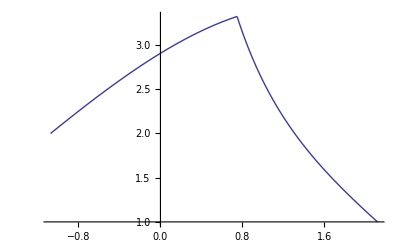

```mathematica
BothGeos=Show[ParametricPlot[{x1Geo[v],rGeo[v]}/.solnGeoUp,{v,0,vTrans},AspectRatio->1/GoldenRatio],ParametricPlot[{x1Geo[v],rGeo[v]}/.solnGeoDown,{v,0,EndPoint[solnGeoDown]},AspectRatio->1/GoldenRatio],PlotRange->All,AxesOrigin->{0,1}]
```

```mathematica
InitialConditionsNewWithEndpointRule=Flatten[{Table[x1N[j][0]-(x1N[j][vTrans]/.soln),{j,0,NumPoints-1}],Table[PxvN[j][0]-(PxvN[j][vTrans]/.soln),{j,0,NumPoints-1}]}]/.AdSSchRules/.(ϵ->-1)/.solnGeoDown;
```

```mathematica
AllExpressionsNewWithEndpointRule=Flatten[{AllDiscretizationsWithEndpointRule,InitialConditionsNewWithEndpointRule}]/.AdSSchRules/.(ϵ->-1)/.solnGeoDown;
```

```mathematica
ndsArgsNewWithEndpointRule={Table[AllExpressionsNewWithEndpointRule[[i]]==0,{i,1,Length[AllExpressionsNewWithEndpointRule]}],AllDiscreteVars,{v,0,EndPoint[solnGeoDown]}};
solnNewWithEndpointRule=Apply[NDSolve,ndsArgsNewWithEndpointRule][[1]];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point v == 0.3896.

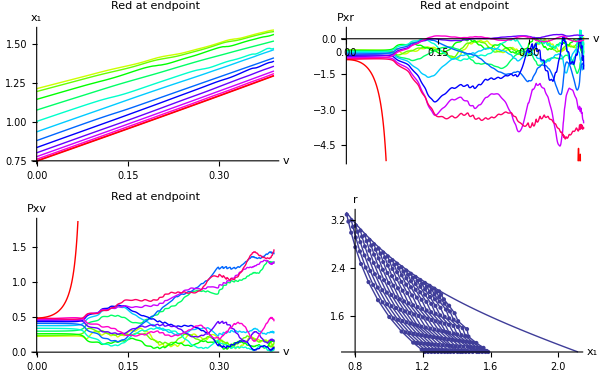

```mathematica
xNPlots=Plot[Evaluate[Flatten[{Table[x1N[i][v]/.solnNewWithEndpointRule,{i,0,NumPoints-1}],x1Geo[v]/.solnGeoDown}]],{v,0,EndPoint[solnNewWithEndpointRule]},AxesLabel->{"v","x_1"},PlotStyle->Table[Hue[0.2+0.8i/NumPoints],{i,0,NumPoints}],PlotLabel->"Red at endpoint"];
PxrPlots=Plot[Evaluate[Table[PxrN[i][v]/.solnNewWithEndpointRule,{i,0,NumPoints}]],{v,0,EndPoint[solnNewWithEndpointRule]},AxesLabel->{"v","Pxr"},PlotStyle->Table[Hue[0.2+0.8i/NumPoints],{i,0,NumPoints}],PlotLabel->"Red at endpoint"];
PxvPlots=Plot[Evaluate[Flatten[{Table[PxvN[i][v]/.solnNewWithEndpointRule,{i,0,NumPoints}]}]],{v,0,EndPoint[solnNewWithEndpointRule]},AxesLabel->{"v","Pxv"},PlotStyle->Table[Hue[0.2+0.8i/NumPoints],{i,0,NumPoints}],PlotLabel->"Red at endpoint"];
StringPlotsNewWithEndpointRule=Show[ShowGeo[solnGeoDown],Table[ListPlot[Table[{x1N[j][v],rN[j][v]},{j,0,NumPoints-1}]/.rGaugeTable/.solnGeoDown/.AdSSchRules/.solnNewWithEndpointRule/.{v->vFrac EndPoint[solnNewWithEndpointRule]},PlotRange->{{-1,6},{0.9,4}},AxesOrigin->{0,1},Joined->True,Mesh->Full],{vFrac,0,1,0.05}],AxesLabel->{"x_1","r"}];
GraphicsGrid[{{xNPlots,PxrPlots},{PxvPlots,StringPlotsNewWithEndpointRule}},ImageSize->600]
```

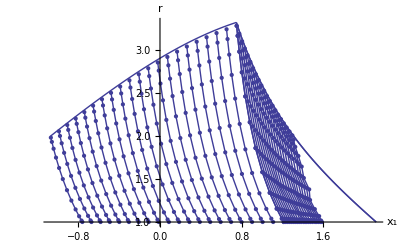

```mathematica
StringPlotsTogetherWithEndpointRule=Show[BothGeos,Table[ListPlot[Table[{x1N[j][v],rN[j][v]},{j,0,NumPoints-1}]/.rGaugeTable/.solnGeoUp/.AdSSchRules/.soln/.{v->vFrac vTrans},PlotRange->{{-1,6},{0.9,4}},AxesOrigin->{0,1},Joined->True,Mesh->Full],{vFrac,0,1,0.05}],StringPlotsNewWithEndpointRule,AxesLabel->{"x_1","r"}]
```

We see that the code does a bit better in terms of the embedding function than the previous one, but still we have the Pxv ‘peel off’.

However, let’s try to use the Pxv without the EndPointRule:

```mathematica
InitialConditionsNewWithoutEndpointRule=Flatten[{Table[x1N[j][0]-(x1N[j][vTrans]/.soln),{j,0,NumPoints-1}],Table[PxvN[j][0]-(PxvN[j][vTrans]/.soln),{j,0,NumPoints}]}]/.AdSSchRules/.(ϵ->-1)/.solnGeoDown;
```

```mathematica
AllExpressionsNewWithoutEndpointRule=Flatten[{AllDiscretizationsWithoutEndpointRule,InitialConditionsNewWithoutEndpointRule}]/.AdSSchRules/.(ϵ->-1)/.solnGeoDown;
```

```mathematica
ndsArgsNewWithoutEndpointRule={Table[AllExpressionsNewWithoutEndpointRule[[i]]==0,{i,1,Length[AllExpressionsNewWithoutEndpointRule]}],AllDiscreteVars,{v,0,EndPoint[solnGeoDown]}};
solnNewWithoutEndpointRule=Apply[NDSolve,ndsArgsNewWithoutEndpointRule][[1]];
```

NDSolve::ndsz: At v == 0.890188, step size is effectively zero; singularity or stiff system suspected.

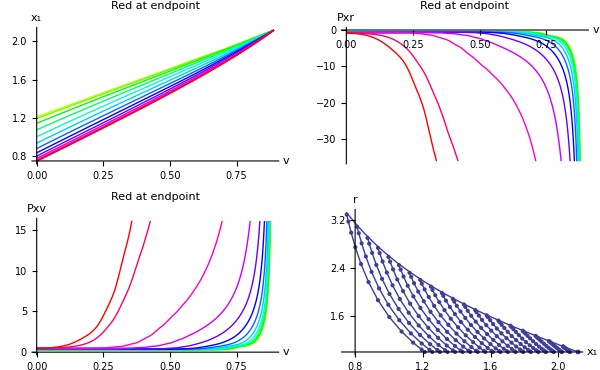

```mathematica
xNPlots=Plot[Evaluate[Flatten[{Table[x1N[i][v]/.solnNewWithoutEndpointRule,{i,0,NumPoints-1}],x1Geo[v]/.solnGeoDown}]],{v,0,EndPoint[solnNewWithoutEndpointRule]},AxesLabel->{"v","x_1"},PlotStyle->Table[Hue[0.2+0.8i/NumPoints],{i,0,NumPoints}],PlotLabel->"Red at endpoint"];
PxrPlots=Plot[Evaluate[Table[PxrN[i][v]/.solnNewWithoutEndpointRule,{i,0,NumPoints}]],{v,0,EndPoint[solnNewWithoutEndpointRule]},AxesLabel->{"v","Pxr"},PlotStyle->Table[Hue[0.2+0.8i/NumPoints],{i,0,NumPoints}],PlotLabel->"Red at endpoint"];
PxvPlots=Plot[Evaluate[Flatten[{Table[PxvN[i][v]/.solnNewWithoutEndpointRule,{i,0,NumPoints}]}]],{v,0,EndPoint[solnNewWithoutEndpointRule]},AxesLabel->{"v","Pxv"},PlotStyle->Table[Hue[0.2+0.8i/NumPoints],{i,0,NumPoints}],PlotLabel->"Red at endpoint"];
StringPlotsNewWithoutEndpointRule=Show[ShowGeo[solnGeoDown],Table[ListPlot[Table[{x1N[j][v],rN[j][v]},{j,0,NumPoints-1}]/.rGaugeTable/.solnGeoDown/.AdSSchRules/.solnNewWithoutEndpointRule/.{v->vFrac EndPoint[solnNewWithoutEndpointRule]},PlotRange->{{-1,6},{0.9,4}},AxesOrigin->{0,1},Joined->True,Mesh->Full],{vFrac,0,1,0.05}],AxesLabel->{"x_1","r"}];
GraphicsGrid[{{xNPlots,PxrPlots},{PxvPlots,StringPlotsNewWithoutEndpointRule}},ImageSize->600]
```

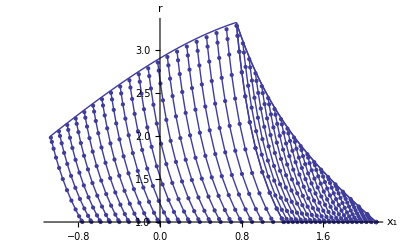

```mathematica
StringPlotsTogetherWithoutEndpointRule=Show[BothGeos,Table[ListPlot[Table[{x1N[j][v],rN[j][v]},{j,0,NumPoints-1}]/.rGaugeTable/.solnGeoUp/.AdSSchRules/.soln/.{v->vFrac vTrans},PlotRange->{{-1,6},{0.9,4}},AxesOrigin->{0,1},Joined->True,Mesh->Full],{vFrac,0,1,0.05}],StringPlotsNewWithoutEndpointRule,AxesLabel->{"x_1","r"}]
```

```mathematica
Export["stringfullplot.pdf",StringPlotsTogetherWithoutEndpointRule]
```

stringfullplot.pdf